```mathematica
sizeEstimates=Table[in=0;
For[n=0,n<1*^5,n++,
c=RandomComplex[{-2,.5+1.5I}];
If[Quiet@MandelbrotSetMemberQ[c],in++;];
];
in/n*2.5*1.5*2,10]
Needs["HypothesisTesting`"];
MeanCI[sizeEstimates]
```

{1.50525,1.49648,1.51177,1.52363,1.53315,1.51665,1.5081,1.51448,1.51845,1.51553}

{0.000047889,0.000337352}

1.5075

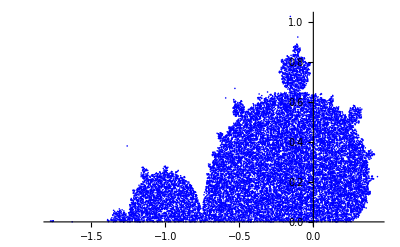

```mathematica
ins={};
For[n=0,n<1*^5,n++,
c=RandomComplex[{-2,.5+1.5I}];
If[Quiet@MandelbrotSetMemberQ[c],AppendTo[ins,c]];
];
Length[ins]/n*2.5*1.5*2
ListPlot[{Re[#],Im[#]}&/@ins,PlotStyle->Blue]
```